```mathematica
(1+Cos[π x])/2
```

1/2 (1+Cos[π x])

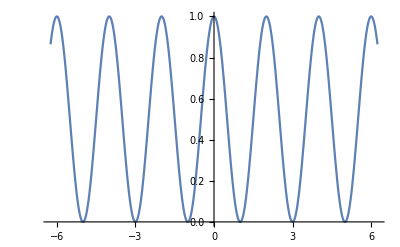

```mathematica
Plot[1/2 (1+Cos[π x]),{x,-6.24,6.24}]
```

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].
Normalize[{1-x,1-f[x]}]==(1+Cos[π x])/2
,{x,f[x],f'[x]}∈Reals]
```

(1-x-(-1+f[x]) f'[x])/(√(((-1+x)^2+(-1+f[x])^2) (1+f'[x]^2)))==Cos[(π x)/2]^2

```mathematica
DSolve[(1-x-(-1+f[x]) f'[x])/(√(((-1+x)^2+(-1+f[x])^2) (1+f'[x]^2)))==Cos[(π x)/2]^2,{f[x]},{x}]
```

$Aborted

```mathematica
DSolve[{(1-x-(-1+f[x]) f'[x])/(√(((-1+x)^2+(-1+f[x])^2) (1+f'[x]^2)))==Cos[(π x)/2]^2,f[0]==0,f[1]==1},{f[x]},{x}]
```

$Aborted

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].
Normalize[{1,1}]==(1+Cos[π x])/2
,{x,f[x],f'[x]}∈Reals]
```

(1+Cos[π x]) √(1+f'[x]^2)==√2 (1+f'[x])

```mathematica
DSolve[(1+Cos[π x]) √(1+f'[x]^2)==√2 (1+f'[x]),{f[x]},{x}]
```

$Aborted

```mathematica
DSolve[{(1+Cos[π x]) √(1+f'[x]^2)==√2 (1+f'[x]),f[0]==0,f[1]==1},{f[x]},{x}]
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

{}

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].
Normalize[{1,1}]==1
,{x,f[x],f'[x]}∈Reals]
```

(1+f'[x])/(√2 √(1+f'[x]^2))==1

```mathematica
DSolve[(1+f'[x])/(√2 √(1+f'[x]^2))==1,{f[x]},{x}]
```

{{f[x]→x+C[1]}}

```mathematica
DSolve[{(1+f'[x])/(√2 √(1+f'[x]^2))==1,f[0]==0,f[1]==1},{f[x]},{x}]
```

{{f[x]→x}}

```mathematica
MemoryInUse[]
```

246784408

```mathematica
√(x'[t]^2+y'[t]^2)
```

√(x'[t]^2+y'[t]^2)

```mathematica
D[√(x'[t]^2+y'[t]^2),y[t]]-D[D[√(x'[t]^2+y'[t]^2),y'[t]],t]==0
```

-y''[t]/(√(x'[t]^2+y'[t]^2))+(y'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0

```mathematica
DSolve[%14,{x[t],y[t],x[t],y[t]},{t}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[-y''[t]/(√(x'[t]^2+y'[t]^2))+(y'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0,{x[t],y[t],x[t],y[t]},{t}]

```mathematica
D[√(x'[t]^2+y'[t]^2),x[t]]-D[D[√(x'[t]^2+y'[t]^2),x'[t]],t]==0
```

-x''[t]/(√(x'[t]^2+y'[t]^2))+(x'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0

```mathematica
DSolve[{-y''[t]/(√(x'[t]^2+y'[t]^2))+(y'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0,-x''[t]/(√(x'[t]^2+y'[t]^2))+(x'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0},{x[t],y[t]},{t}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

DSolve[{-y''[t]/(√(x'[t]^2+y'[t]^2))+(y'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0,-x''[t]/(√(x'[t]^2+y'[t]^2))+(x'[t] (2 x'[t] x''[t]+2 y'[t] y''[t]))/(2 (x'[t]^2+y'[t]^2)^(3/2))==0},{x[t],y[t]},{t}]

```mathematica
D[y[x] √(1+y'[x]^2),y[x]]-D[D[y[x] √(1+y'[x]^2),y'[x]],x]==0
```

-y'[x]^2/(√(1+y'[x]^2))+√(1+y'[x]^2)+(y[x] y'[x]^2 y''[x])/((1+y'[x]^2)^(3/2))-(y[x] y''[x])/(√(1+y'[x]^2))==0

```mathematica
DSolve[%18,{y[x],y[x]},{x}]
```

{{y[x]→-(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))},{y[x]→(ⅇ^(-C[1]) Tanh[ⅇ^C[1] (x+C[2])])/(√(-1+Tanh[ⅇ^C[1] (x+C[2])]^2))}}

```mathematica
(ⅇ^-1 Tanh[ⅇ (x+1)])/(√(-1+Tanh[ⅇ (x+1)]^2))
```

Tanh[ⅇ (1+x)]/(ⅇ √(-1+Tanh[ⅇ (1+x)]^2))

```mathematica
FullSimplify[Tanh[ⅇ (1+x)]/(ⅇ √(-1+Tanh[ⅇ (1+x)]^2))]
```

Tanh[ⅇ (1+x)]/(ⅇ √(-Sech[ⅇ (1+x)]^2))

```mathematica
Plot[Tanh[ⅇ (1+x)]/(ⅇ √(-Sech[ⅇ (1+x)]^2)),{x,-2,2}]
```

-Graphics-

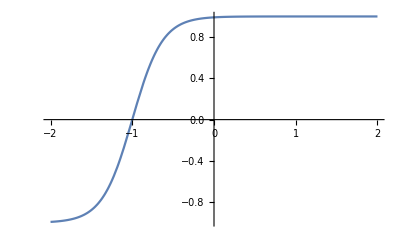

```mathematica
Plot[Tanh[ⅇ (1+x)],{x,-2,2}]
```

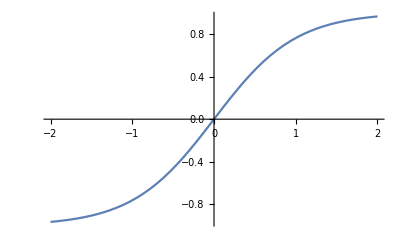

```mathematica
Plot[Tanh[x],{x,-2,2}]
```

```mathematica
FullSimplify[
Normalize[{1,f'[x]}]
,{x,f'[x]}∈Reals]
```

{1/(√(1+f'[x]^2)),f'[x]/(√(1+f'[x]^2))}

```mathematica
FullSimplify[
Normalize[{1,f'[x]}].Normalize[{1,g'[x]}]==1
,{x,f'[x],g'[x]}∈Reals]
```

√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x]

```mathematica
DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{f[x],g[x]},{x}]

```mathematica
DSolve[√((1+f'[x]^2) (1+g'[x]^2))==1+f'[x] g'[x],{g[x]},{x}]
```

{{g[x]→C[1]+f[x]}}

```mathematica
FullSimplify[
Normalize[{α,f'[x]}].Normalize[{1,g'[x]}]==1
,{α,x,f'[x],g'[x]}∈Reals]
```

(α+f'[x] g'[x])/(√((α^2+f'[x]^2) (1+g'[x]^2)))==1

```mathematica
DSolve[(α+f'[x] g'[x])/(√((α^2+f'[x]^2) (1+g'[x]^2)))==1,{f[x],g[x]},{x}]
```

DSolve::underdet: There are more dependent variables than equations, so the system is underdetermined.

DSolve[(α+f'[x] g'[x])/(√((α^2+f'[x]^2) (1+g'[x]^2)))==1,{f[x],g[x]},{x}]

```mathematica
DSolve[(α+f'[x] g'[x])/(√((α^2+f'[x]^2) (1+g'[x]^2)))==1,{g[x]},{x}]
```

{{g[x]→C[1]+f[x]/α}}

```mathematica
Tanh[x]
```

Tanh[x]

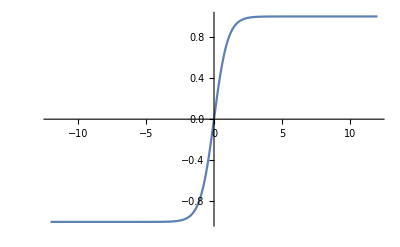

```mathematica
Plot[Tanh[x],{x,-12.,12.}]
```

```mathematica
FullSimplify[
Normalize[{x,x}].Normalize[{1,g'[x]}]==1
,{α,x,f'[x]}∈Reals]
```

2 √(1+Abs[g'[x]]^2)==√2 Sign[x] (1+g'[x])

```mathematica
DSolve[2 √(1+Abs[g'[x]]^2)==√2 Sign[x] (1+g'[x]),{g[x]},{x}]
```

{{g[x]→C[1]+(-Sign[K[1]]^2-2 √(-1+Sign[K[1]]^2))/(-2+Sign[K[1]]^2)K[1]1x},{g[x]→C[1]+(-Sign[K[2]]^2+2 √(-1+Sign[K[2]]^2))/(-2+Sign[K[2]]^2)K[2]1x}}

```mathematica
FullSimplify[
Normalize[{x,x}].Normalize[{1,g'[x]}]==Tanh[x]
,{α,x,f'[x]}∈Reals]
```

√2 Sign[x] (1+g'[x])==2 √(1+Abs[g'[x]]^2) Tanh[x]

```mathematica
DSolve[√2 Sign[x] (1+g'[x])==2 √(1+Abs[g'[x]]^2) Tanh[x],{g[x]},{x}]
```

{{g[x]→C[1]+(-2 Cosh[K[1]]^2 Sign[K[1]]^2-√(16 Cosh[K[1]]^2 Sign[K[1]]^2 Sinh[K[1]]^2-16 Sinh[K[1]]^4))/(2 (Cosh[K[1]]^2 Sign[K[1]]^2-2 Sinh[K[1]]^2))K[1]1x},{g[x]→C[1]+(-2 Cosh[K[2]]^2 Sign[K[2]]^2+√(16 Cosh[K[2]]^2 Sign[K[2]]^2 Sinh[K[2]]^2-16 Sinh[K[2]]^4))/(2 (Cosh[K[2]]^2 Sign[K[2]]^2-2 Sinh[K[2]]^2))K[2]1x}}

```mathematica
g[x]/.%37
```

{C[1]+(-2 Cosh[K[1]]^2 Sign[K[1]]^2-√(16 Cosh[K[1]]^2 Sign[K[1]]^2 Sinh[K[1]]^2-16 Sinh[K[1]]^4))/(2 (Cosh[K[1]]^2 Sign[K[1]]^2-2 Sinh[K[1]]^2))K[1]1x,C[1]+(-2 Cosh[K[2]]^2 Sign[K[2]]^2+√(16 Cosh[K[2]]^2 Sign[K[2]]^2 Sinh[K[2]]^2-16 Sinh[K[2]]^4))/(2 (Cosh[K[2]]^2 Sign[K[2]]^2-2 Sinh[K[2]]^2))K[2]1x}

```mathematica
(-2 Cosh[K[1]]^2 Sign[K[1]]^2-√(16 Cosh[K[1]]^2 Sign[K[1]]^2 Sinh[K[1]]^2-16 Sinh[K[1]]^4))/(2 (Cosh[K[1]]^2 Sign[K[1]]^2-2 Sinh[K[1]]^2))K[1]1x
```

(-2 Cosh[K[1]]^2 Sign[K[1]]^2-√(16 Cosh[K[1]]^2 Sign[K[1]]^2 Sinh[K[1]]^2-16 Sinh[K[1]]^4))/(2 (Cosh[K[1]]^2 Sign[K[1]]^2-2 Sinh[K[1]]^2))K[1]1x

```mathematica
Activate[Out[39]]
```

$Aborted

```mathematica
Activate[(-Sign[K[1]]^2-2 √(-1+Sign[K[1]]^2))/(-2+Sign[K[1]]^2)K[1]1x]
```

ConditionalExpression[-1+x,x∈ℝ]